Your Title Here

```mathematica
w1=5;w2=7;h1=3;h2=5;L=2*(w1+w2);H=h1+h2;
```

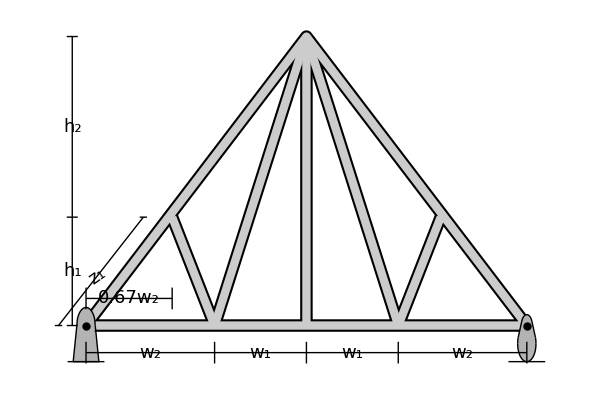

```mathematica
truss=Graphics[{Thick,
{Thickness@#1,#2,Line[{{w2,0},{0.67*w2,h1}}],Line[{{w2,0},{w1+w2,H}}],Line[{{2*w1+w2,0},{L-0.67*w2,h1}}],Line[{{2*w1+w2,0},{w1+w2,H}}],Line[{{w1+w2,0},{w1+w2,H}}],
EdgeForm@{Thickness@#1,#2},FaceForm@None,Polygon[{{0,0},{L,0},{w1+w2,H}}]}&@@@{{0.015,Black},{0.01,GrayLevel@0.8}},

{GrayLevel@0.7,
Polygon[{{-0.7,-1},{0.7,-1},{0.5,0},{-0.5,0}}],Disk[{0,0},0.5],
Disk[{L,0},0.3],Disk[{L,-0.5},0.5],Polygon[{{L-0.275,0.12},{L+0.275,0.12},{L+0.47,-0.33},{L-0.47,-0.33}}]
},
{Thin,Line[{{-0.5,0},{-0.7,-1},{0.7,-1},{0.5,0}}],Line[{#,√(0.5^2-#^2)}&/@Range[-0.5,0.5,0.02]],
Line[{{L+#*0.275,0.12},{L+#*0.47,-0.33}}]&/@{-1,1},
Line[{#,√(0.3^2-(#-L)^2)}&/@Range[L-0.275,L+0.275,0.01]],Line[{#,-√(0.5^2-(#-L)^2)-0.5}&/@Range[L-0.5,L+0.5,0.01]],
Line[{#,√(0.5^2-(#-L)^2)-0.5}&/@Range[L-0.5,L-0.47,0.01]],Line[{#,√(0.5^2-(#-L)^2)-0.5}&/@Range[L+0.47,L+0.5,0.01]],
Line[{{#-1,-1},{#+1,-1}}]&/@{0,L}},

{PointSize@0.01,Point@{#,0}}&/@{0,L},

{Thin,
Line[{{0,0.25*h1},{0.67*w2,0.25*h1}}],Line[{{#,0.15*h1},{#,0.35*h1}}]&/@{0,0.67*w2},
Text[Style[Row@{"0.67",Subscript[Style[" w",Italic],2]},18,Background->White],{0.67*w2/2,0.25*h1}],

Line[{{0,-0.25*h1},{2*(w1+w2),-0.25*h1}}],Line[{{#,-0.15*h1},{#,-0.35*h1}}]&/@{0,w2,w1+w2,2*w1+w2,2*(w1+w2)},
Text[Style[Subscript[Style[" w",Italic],#1],18,Background->White],{#2,-0.25*h1}]&@@@{{2,w2/2},{1,w2+w1/2},{1,1.5*w1+w2},{2,2*w1+1.5*w2}},

Line[{{-0.25*h1,0},{-0.25*h1,h1+h2}}],Line[{{-0.15*h1,#},{-0.35*h1,#}}]&/@{0,h1,h1+h2},
Text[Style[Subscript[Style["h",Italic],#1],18,Background->White],{-0.25*h1,#2}]&@@@{{1,h1/2},{2,h1+h2/2}},

Line[{{-1.5,0},{0.66*w2-1.5,h1}}],Line[{{-1.3,0},{-1.7,0}}],Line[{{0.66*w2-1.3,h1},{0.66*w2-1.7,h1}}],
(*Text[Rotate[Style["√((SubscriptBox[h, 1])^2)",10,Background->White],ArcTan[h1/(0.6*w2)]],{0.6225,1.362}]*)
Text[Rotate[Style["z_1",18,Background->White],ArcTan[h1/(0.6*w2)]],{0.6225,1.362}]
}
},ImageSize->{600,400}]
```

```mathematica
Graphics[{Thick,
Line[{{0,0},{w1,0}}],
},ImageSize->{600,425}]
```





```mathematica
Manipulate[
Module[{θ1,scale,forces,members},
θ1=ArcTan[h1/(0.33*w2)];

(*sol=Solve[{
fab*Sin[θ]+ra
},][[1]];*)

scale[F_]:=1.5+5*Rescale[F,{0,10}];

forces={Blue,
Arrow[{{0.67*w2-scale[FA]*Cos[θ1],h1+scale[FA]*Sin[θ1]},{0.67*w2,h1}}],Arrow[{{w1+w2,h1+h2+scale[FB]},{w1+w2,h1+h2}}],
Text[Style[Row@{Subscript[Style["F",Italic],#1]," = ",NumberForm[#2,{3,1}]," kN"},18,Blue],#3,#4]&@@@{{"A",FA,{0.67*w2-scale[FA]*Cos[θ1],h1+scale[FA]*Sin[θ1]},{0.,-1}},{"B",FB,{w1+w2,h1+h2+scale[FB]},{0,-1.5}}}};

members={
{Thickness@0.015,Red,CapForm@"Round",Switch[member,1,Line[{{0,0},{0.66*w2,h1}}],2,Line[{{0,0},{w2,0}}],3,Line[{{w2,0},{0.67*w2,h1}}],
4,Line[{{0.67*w2,h1},{w1+w2,H}}],5,Line[{{w2,0},{w1+w2,H}}],6,Line[{{w2,0},{w1+w2,0}}],7,Line[{{w1+w2,0},{w1+w2,H}}],
8,Line[{{w1+w2,H},{2*w1+w2+0.33*w2,h1}}],9,Line[{{w1+w2,H},{2*w1+w2,0}}],10,Line[{{w1+w2,0},{2*w1+w2,0}}],
11,Line[{{2*w1+w2,0},{2*w1+w2+0.33*w2,h1}}],12,Line[{{2*w1+w2+0.33*w2,h1},{L,0}}],13,Line[{{2*w1+w2,0},{L,0}}]]},

Text[Framed[Style[Row@{" ",#1," "},17],Background->White,RoundingRadius->15,FrameMargins->Tiny],#2]&@@@{{1,{0.66*w2/2,h1/2}},{2,{w2/2,0}},{3,{(0.67*w2+w2)/2,h1/2}},{4,{0.67*w2+(0.33*w2+w1)/2,h1+h2/2}},{5,{w2+w1/2,H/2}},{6,{w2+w1/2,0}},{7,{w1+w2,H/2}},{8,{w1+w2+(w1+0.33*w2)/2,h1+h2/2}},{9,{1.5*w1+w2,H/2}},{10,{1.5*w1+w2,0}},{11,{2*w1+w2+0.33*w2/2,h1/2}},{12,{2*w1+w2+(0.33*w2+w2)/2,h1/2}},{13,{2*w1+1.5*w2,0}}},
};

Show[truss,PlotRange->{{-6.2,25.15},{-6.3,13.75}},(*{-1.15,15.8},*)Epilog->{Thick,Arrowheads@0.045,forces,(*members*)
Blue,Arrow[{{0,-scale[5]},{0,0}}],Arrow[{{-scale[5],0},{0,0}}],Arrow[{{2*(w1+w2),-scale[5]},{2*(w1+w2),0}}],
Text[Style[Subscript[Style["R",Italic],Row@{"A,",Style[#1,Italic]}],18],#2,#3]&@@@{{"x",{-scale[5],0},{1.5,0}},{"y",{0,-scale[5]},{0,1.5}}},
Text[Style[Subscript[Style["R",Italic],"E"],18],{2*(w1+w2),-scale[5]},{0,1.5}]
}]
],
Grid[{
{Control[{{member,1,"member"},{1->" 1 ",2->" 2 ",3->" 3 ",4->" 4 ",5->" 5 ",6->" 6 ",7->" 7 ",8->" 8 ",9->" 9 ",10->" 10 ",11->" 11 ",12->" 12 ",13->" 13 "},Setter}],SpanFromLeft},
{Style["point load forces (kN)",Bold],
Control[{{FA,2,"diagonal"},0,5,0.1,Appearance->"Labeled",ImageSize->Small}],
Control[{{FB,5,"vertical"},0,10,0.1,Appearance->"Labeled",ImageSize->Small}]}
},Alignment->Left],
SaveDefinitions->True]
```

Resize Images

Rotate and Zoom in 3D

Drag Locators

Create and Delete Locators

Slider Zoom

Gamepad Controls

Automatic Animation

Bookmark Animation

Contributed by: XXXX